## Rp-Rm-approach

```mathematica
ClearAll["Global`*"];
(*FpFm - equations*)
eq1=κ(1+I α)(G+d-1)Fp-(γa+I γp)Fm+Sqrt[κ Csp (G+d+T)] (ξ1r+I ξ1i);
eq2=κ(1+I α)(G-d-1)Fm-(γa+I γp)Fp+Sqrt[κ Csp (G-d+T)] (ξ2r+I ξ2i);
eq3=γ(μ-G)-γ G(Abs[Fp]^2+Abs[Fm]^2)-γ d (Abs[Fp]^2-Abs[Fm]^2);
eq4=-γd d-γ G(Abs[Fp]^2-Abs[Fm]^2)-γ d (Abs[Fp]^2+Abs[Fm]^2);
```

```mathematica
Rsubs={Fp-> Fpr+I Fpi,Fm-> Fmr+I Fmi};Eq1=Expand[(eq1/.Rsubs)]//Re//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T+d>0&&κ>0&&Csp>0}]&;
Eq2=Expand[(eq1/.Rsubs)]//Im//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T+d>0&&κ>0&&Csp>0}]&;
Eq3=Expand[(eq2/.Rsubs)]//Re//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T-d>0&&κ>0&&Csp>0}]&;
Eq4=Expand[(eq2/.Rsubs)]//Im//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T-d>0&&κ>0&&Csp>0}]&;
Eqs={Eq1,Eq2,Eq3,Eq4};
```

```mathematica
Eqvars={Fpr,Fpi,Fmr,Fmi};
Eqnoise={ξ1r,ξ1i,ξ2r,ξ2i};
Coefs=Table[CoefficientList[Eqs[[i]],Eqnoise[[i]]],{i,1,4}];
```

```mathematica
Qvarexpl={Sqrt[Fpr^2+Fpi^2],ArcTan[Fpi/Fpr]-ω t,Sqrt[Fmr^2+Fmi^2],ArcTan[Fmi/Fmr]-ω t};
EqQ=Table[D[Qvarexpl[[i]],t]+Sum[D[Qvarexpl[[i]],Eqvars[[j]]] Coefs[[j,1]],{j,1,4}]+1/2 Sum[D[Qvarexpl[[i]],{Eqvars[[j]],2}]Coefs[[j,2]]^2,{j,1,4}],{i,1,4}]//FullSimplify;
FfQsub={Fpr-> Rp*Cos[ϕp+ωt],Fpi-> Rp*Sin[ϕp+ωt],Fmr-> Rm*Cos[ϕm+ωt],Fmi-> Rm*Sin[ϕm+ωt]};
EqQsimple=EqQ/.FfQsub//FullSimplify[#,Assumptions->{Rm>0&&Rp>0}]&;
EqQdiff=Table[Sum[D[Qvarexpl[[i]],Eqvars[[j]]] Coefs[[j,2]] Eqnoise[[j]],{j,1,4}],{i,1,4}]/.FfQsub//FullSimplify[#,Assumptions->{Rm>0&&Rp>0}]&;
EqQsimple/.{ϕm-ϕp-> -ψ}//FullSimplify//MatrixForm
```

((-1+d+G) Rp κ+(Csp (d+G+T) κ)/(2 Rp)-Rm (γa Cos[ψ]+γp Sin[ψ])
((-1+d+G) Rp α κ-Rp ω-Rm γp Cos[ψ]+Rm γa Sin[ψ])/Rp
(-1-d+G) Rm κ+(Csp (-d+G+T) κ)/(2 Rm)-Rp γa Cos[ψ]+Rp γp Sin[ψ]
-(Rm ((1+d-G) α κ+ω)+Rp γp Cos[ψ]+Rp γa Sin[ψ])/Rm)

```mathematica
Dmatrix=(KroneckerProduct[EqQdiff,EqQdiff]/2//Expand)/.({Table[Eqnoise[[i]] Eqnoise[[j]]-> KroneckerDelta[i,j],{i,1,4},{j,1,4}],Table[Eqnoise[[i]]-> 0,{i,1,4}]}//Flatten)//FullSimplify;
Dmatrix//MatrixForm
```

(1/2 Csp (d+G+T) κ | 0 | 0 | 0
0 | (Csp (d+G+T) κ)/(2 Rp^2) | 0 | 0
0 | 0 | 1/2 Csp (-d+G+T) κ | 0
0 | 0 | 0 | (Csp (-d+G+T) κ)/(2 Rm^2))

```mathematica
EqQs={EqQsimple,{eq3,eq4}/.Rsubs/.FfQsub//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&_Symbol∈Reals}]&}//Flatten;
(*ϕp = ϕ, ϕm=ϕ-ψ*)
newvarsub={ϕm-ϕp->- ψ,ϕp-ϕm->ψ,G-> (Np+Nm)/2,d->( Np-Nm)/2};
transf={
{1,0,0,0,0,0},
{0,0,1,0,0,0},
{0,1,0,0,0,0},
{0,1,0,-1,0,0},
{0,0,0,0,1,1},
{0,0,0,0,1,-1}
};
EqQs=transf.EqQs/.newvarsub//FullSimplify[#,Assumptions->{Rp>0&&Rm>0&&_Symbol∈Reals}]&;
```

```mathematica
EqQs//MatrixForm
```

((-1+Np) Rp κ+(Csp (Np+T) κ)/(2 Rp)-Rm (γa Cos[ψ]+γp Sin[ψ])
(-1+Nm) Rm κ+(Csp (Nm+T) κ)/(2 Rm)-Rp γa Cos[ψ]+Rp γp Sin[ψ]
((-1+Np) Rp α κ-Rp ω-Rm γp Cos[ψ]+Rm γa Sin[ψ])/Rp
((-Nm+Np) Rm Rp α κ+(-Rm^2+Rp^2) γp Cos[ψ]+(Rm^2+Rp^2) γa Sin[ψ])/(Rm Rp)
1/2 (Nm (-γ+γd)-Np (γ+4 Rp^2 γ+γd)+2 γ μ)
1/2 (Np (-γ+γd)-Nm (γ+4 Rm^2 γ+γd)+2 γ μ))

```mathematica
EqQsDiff=ConstantArray[0,{6,6}];
EqQsDiff[[1;;4,1;;4]]=Dmatrix;
EqQsDiff = transf.EqQsDiff.Transpose[transf]/.newvarsub//FullSimplify;
EqQsDiff//MatrixForm
```

(1/2 Csp (Np+T) κ | 0 | 0 | 0 | 0 | 0
0 | 1/2 Csp (Nm+T) κ | 0 | 0 | 0 | 0
0 | 0 | (Csp (Np+T) κ)/(2 Rp^2) | (Csp (Np+T) κ)/(2 Rp^2) | 0 | 0
0 | 0 | (Csp (Np+T) κ)/(2 Rp^2) | (Csp (Np Rm^2+Rm^2 T+Rp^2 (Nm+T)) κ)/(2 Rm^2 Rp^2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*We will use time scale t->γ t, so now all decay rates are normalized on γ and ω=ω/γ*)
EqQs=EqQs/.{γ->1};
EqQs//MatrixForm
EqQsDiff//MatrixForm
```

((-1+Np) Rp κ+(Csp (Np+T) κ)/(2 Rp)-Rm (γa Cos[ψ]+γp Sin[ψ])
(-1+Nm) Rm κ+(Csp (Nm+T) κ)/(2 Rm)-Rp γa Cos[ψ]+Rp γp Sin[ψ]
((-1+Np) Rp α κ-Rp ω-Rm γp Cos[ψ]+Rm γa Sin[ψ])/Rp
((-Nm+Np) Rm Rp α κ+(-Rm^2+Rp^2) γp Cos[ψ]+(Rm^2+Rp^2) γa Sin[ψ])/(Rm Rp)
1/2 (Nm (-1+γd)-Np (1+4 Rp^2+γd)+2 μ)
1/2 (Np (-1+γd)-Nm (1+4 Rm^2+γd)+2 μ))

(1/2 Csp (Np+T) κ | 0 | 0 | 0 | 0 | 0
0 | 1/2 Csp (Nm+T) κ | 0 | 0 | 0 | 0
0 | 0 | (Csp (Np+T) κ)/(2 Rp^2) | (Csp (Np+T) κ)/(2 Rp^2) | 0 | 0
0 | 0 | (Csp (Np+T) κ)/(2 Rp^2) | (Csp (Np Rm^2+Rm^2 T+Rp^2 (Nm+T)) κ)/(2 Rm^2 Rp^2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Qvars={Rp,Rm,ϕ,ψ,G,d};
ff:=f[Rp,Rm,ϕ,ψ,G,d];
Sum[D[EqQs[[j]]*ff,Qvars[[j]]],{j,1,6}]//FullSimplify[#,Assumptions->{Rm>0,Rp>0}]&//Collect[#,ff]&
```

f[Rp,Rm,ϕ,ψ,G,d] (-1-2 Rm^2-2 Rp^2-γd+(-1-d+G) κ+(-1+d+G) κ-(Csp (-d+G+T) κ)/(2 Rm^2)-(Csp (d+G+T) κ)/(2 Rp^2)+((Rm^2+Rp^2) γa Cos[ψ]+(Rm-Rp) (Rm+Rp) γp Sin[ψ])/(Rm Rp))+(G (Rm-Rp) (Rm+Rp)-d (Rm^2+Rp^2+γd)) f^(0,0,0,0,0,1)[Rp,Rm,ϕ,ψ,G,d]+(d (Rm-Rp) (Rm+Rp)-G (1+Rm^2+Rp^2)+μ) f^(0,0,0,0,1,0)[Rp,Rm,ϕ,ψ,G,d]+((2 d Rm Rp α κ+(-Rm^2+Rp^2) γp Cos[ψ]+(Rm^2+Rp^2) γa Sin[ψ]) f^(0,0,0,1,0,0)[Rp,Rm,ϕ,ψ,G,d])/(Rm Rp)+(((-1+d+G) Rp α κ-Rp ω-Rm γp Cos[ψ]+Rm γa Sin[ψ]) f^(0,0,1,0,0,0)[Rp,Rm,ϕ,ψ,G,d])/Rp+((-1-d+G) Rm κ+(Csp (-d+G+T) κ)/(2 Rm)-Rp γa Cos[ψ]+Rp γp Sin[ψ]) f^(0,1,0,0,0,0)[Rp,Rm,ϕ,ψ,G,d]+((-1+d+G) Rp κ+(Csp (d+G+T) κ)/(2 Rp)-Rm (γa Cos[ψ]+γp Sin[ψ])) f^(1,0,0,0,0,0)[Rp,Rm,ϕ,ψ,G,d]

```mathematica
Clear[f]
```

```mathematica
LaguerreL[n,a,x]
```

LaguerreL[n,a,x]

```mathematica
Integrate[LaguerreL[3,1,x]*LaguerreL[k,1,x]*x^(0)*Exp[-x],{x,0,Infinity}]
```

$Aborted

```mathematica
Integrate[1/x*LaguerreL[21,1,x]*x*Exp[-x],{x,0,Infinity}]
```

1

```mathematica
3!/2!
```

3

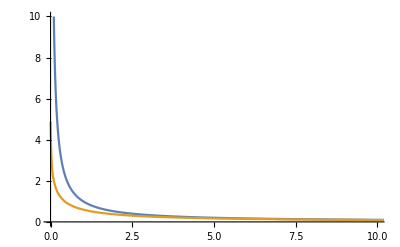

```mathematica
Plot[{1/x,Sum[n!/(n+2)! LaguerreL[n,1,x],{n,0,200}]},{x,0,20},PlotRange->{{0,10},{0,10}}]
```

```mathematica
k=1;
Integrate[x*LaguerreL[0,1,x]^2*Exp[-x],{x,0,Infinity}]
```

1

```mathematica
LaguerreL[1,1,x]
```

2-x

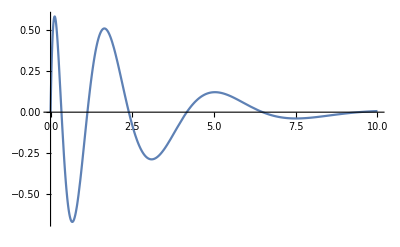

```mathematica
Plot[ LaguerreL[10,1,x]*x*Exp[-x],{x,0,10}]
```

```mathematica
x*LaguerreL[n,α,x]//FunctionExpand
```

x LaguerreL[n,α,x]

```mathematica
k=0;
α=1;
x*D[LaguerreL[k,α,x],x]-(LaguerreL[k-1,α,x]*(k-x-1)-LaguerreL[k-2,α,x]*(k+α-1))//FullSimplify
```

0

```mathematica
k=2;
α=1;
x*D[LaguerreL[k,α,x],x]-(k*LaguerreL[k,α,x]-(α+k)LaguerreL[k-1,α,x])
```

-6+3 (2-x)+6 x-x^2+1/2 x (-6+2 x)

```mathematica
D[LaguerreL[k,α,x],x]//FullSimplify
```

-1/2 (-6+x) (-2+x)

```mathematica
LaguerreL[k-1,α+1,x]//FullSimplify
```

1/2 (-6+x) (-2+x)

```mathematica
x*LaguerreL[k-1,α+1,x]+(LaguerreL[k-1,α,x]*(k-x-1)-LaguerreL[k-2,α,x]*(k+α-1))//FullSimplify
```

0

## Qx-Qy-approach

```mathematica
ClearAll["Global`*"];
(*FxFy equation*)
eq1=κ(1+I α)(I d Fy+Fx (G-1))-Fx (γa+I γp)+Sqrt[κ Csp/2](Sqrt[G+d+T] (ξ1r+I ξ1i)+Sqrt[G-d+T] (ξ2r+I ξ2i));
eq2=κ(1+I α)(-I d Fx+Fy (G-1))+Fy (γa+I γp)+Sqrt[κ Csp/2]/I (Sqrt[G+d+T] (ξ1r+I ξ1i)-Sqrt[G-d+T] (ξ2r+I ξ2i));
eq3=γ(μ-G)-γ G(Abs[Fx]^2+Abs[Fy]^2)-I γ d (Conjugate[Fx] Fy - Conjugate[Fy] Fx);
eq4=-γd d-I γ G (Conjugate[Fx] Fy - Conjugate[Fy] Fx)-γ d (Abs[Fx]^2+Abs[Fy]^2);
```

```mathematica
Rsubs={Fx-> Fxr+I Fxi,Fy-> Fyr+I Fyi};Eq1=Expand[(eq1/.Rsubs)]//Re//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T+d>0&&G+T-d>0&&κ>0&&Csp>0}]&;
Eq2=Expand[(eq1/.Rsubs)]//Im//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T+d>0&&G+T-d>0&&κ>0&&Csp>0}]&;
Eq3=Expand[(eq2/.Rsubs)]//Re//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T+d>0&&G+T-d>0&&κ>0&&Csp>0}]&;
Eq4=Expand[(eq2/.Rsubs)]//Im//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T+d>0&&G+T-d>0&&κ>0&&Csp>0}]&;
Eqs={Eq1,Eq2,Eq3,Eq4};
```

```mathematica
Eqs//MatrixForm
```

(Fxi γp-(Fxi (-1+G) α+d (Fyi+Fyr α)) κ-Fxr (γa+κ-G κ)+(√(Csp (d+G+T) κ) ξ1r+√(Csp (-d+G+T) κ) ξ2r)/(√2)
-Fxr γp+Fxr (-1+G) α κ+d (Fyr-Fyi α) κ-Fxi (γa+κ-G κ)+(√(Csp (d+G+T) κ) ξ1i+√(Csp (-d+G+T) κ) ξ2i)/(√2)
d (Fxi+Fxr α) κ+Fyr (γa+(-1+G) κ)-Fyi (γp+(-1+G) α κ)+(√(Csp (d+G+T) κ) ξ1i-√(Csp (-d+G+T) κ) ξ2i)/(√2)
d (-Fxr+Fxi α) κ+Fyi (γa+(-1+G) κ)+Fyr (γp+(-1+G) α κ)+(-√(Csp (d+G+T) κ) ξ1r+√(Csp (-d+G+T) κ) ξ2r)/(√2))

```mathematica
Eqvars={Fxr,Fxi,Fyr,Fyi};
Eqnoise={ξ1r,ξ1i,ξ2r,ξ2i};
sqDm=Table[CoefficientList[Eqs[[i]],{Eqnoise[[j]]},{2}][[2]],{i,1,4},{j,1,4}];
EqDiffusionMat=sqDm.Transpose[sqDm]//FullSimplify;
EqDriftMat=CoefficientList[Eqs,Eqnoise,{1,1,1,1}]//Flatten;
EqDriftMat//MatrixForm
```

(Fxi γp-(Fxi (-1+G) α+d (Fyi+Fyr α)) κ-Fxr (γa+κ-G κ)
-Fxr γp+Fxr (-1+G) α κ+d (Fyr-Fyi α) κ-Fxi (γa+κ-G κ)
d (Fxi+Fxr α) κ+Fyr (γa+(-1+G) κ)-Fyi (γp+(-1+G) α κ)
d (-Fxr+Fxi α) κ+Fyi (γa+(-1+G) κ)+Fyr (γp+(-1+G) α κ))

```mathematica
Qvarexpl={Fxr^2+Fxi^2,ArcTan[Fxi/Fxr]-ω t,Fyr^2+Fyi^2,ArcTan[Fyi/Fyr]-ω t};
EqQ=Table[D[Qvarexpl[[i]],t]+Sum[D[Qvarexpl[[i]],Eqvars[[j]]] EqDriftMat[[j]],{j,1,4}]+1/2 Sum[D[Qvarexpl[[i]],Eqvars[[j]],Eqvars[[k]]]EqDiffusionMat[[j,k]],{j,1,4},{k,1,4}],{i,1,4}]//FullSimplify;
FfQsub={Fxr-> Sqrt[Qx]*Cos[ϕx+ωt],Fxi-> Sqrt[Qx]*Sin[ϕx+ωt],Fyr-> Sqrt[Qy]*Cos[ϕy+ωt],Fyi-> Sqrt[Qy]*Sin[ϕy+ωt]};
EqQdrift=EqQ/.FfQsub//FullSimplify[#,Assumptions->{Qx>0&&Qy>0}]&;
(*EqQdiffcoef=Table[Sum[D[Qvarexpl[[i]],Eqvars[[k]]]sqDm[[k,j]] Eqnoise[[j]],{k,1,4},{j,1,4}],{i,1,4}]/.FfQsub//FullSimplify[#,Assumptions->{Qx>0&&Qy>0}]&;
EqQsimple/.{ϕm-ϕp-> -2ψ}//FullSimplify//MatrixForm
Dmatrix=(KroneckerProduct[EqQdiffcoef,EqQdiffcoef]//Expand)/.({Table[Eqnoise[[i]] Eqnoise[[j]]-> KroneckerDelta[i,j],{i,1,4},{j,1,4}],Table[Eqnoise[[i]]-> 0,{i,1,4}]}//Flatten)//FullSimplify;
Dmatrix//MatrixForm*)
Jak=Table[D[Qvarexpl[[i]],Eqvars[[j]]],{i,1,4},{j,1,4}]//FullSimplify;
EqQdiff=Jak.EqDiffusionMat.Transpose[Jak]/.FfQsub//FullSimplify[#,Assumptions->{Qx>0&&Qy>0}]&;
EqQdiff//MatrixForm
```

(4 Csp Qx (G+T) κ | 0 | 4 Csp d √(Qx Qy) κ Sin[ϕx-ϕy] | -2 Csp d √(Qx/Qy) κ Cos[ϕx-ϕy]
0 | (Csp (G+T) κ)/Qx | 2 Csp d √(Qy/Qx) κ Cos[ϕx-ϕy] | (Csp d κ Sin[ϕx-ϕy])/(√(Qx Qy))
4 Csp d √(Qx Qy) κ Sin[ϕx-ϕy] | 2 Csp d √(Qy/Qx) κ Cos[ϕx-ϕy] | 4 Csp Qy (G+T) κ | 0
-2 Csp d √(Qx/Qy) κ Cos[ϕx-ϕy] | (Csp d κ Sin[ϕx-ϕy])/(√(Qx Qy)) | 0 | (Csp (G+T) κ)/Qy)

```mathematica
EqQs={EqQdrift,{eq3,eq4}/.Rsubs/.FfQsub//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&_Symbol∈Reals}]&}//Flatten;
(*ϕx = ϕ, ϕy=ϕ-ψ*)
transf={
{1,0,0,0,0,0},
{0,0,1,0,0,0},
{0,1,0,0,0,0},
{0,1,0,-1,0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,1}
};
EqQs=FullSimplify[transf.EqQs,Assumptions->{Qx>0&&Qy>0&&_Symbol∈Reals}]/.{ϕx-ϕy-> ψ,ϕy-ϕx->-ψ};
```

```mathematica
EqQs//MatrixForm
```

(2 Csp (G+T) κ-2 Qx (γa+κ-G κ)+2 d √(Qx Qy) κ (-α Cos[ψ]+Sin[ψ])
2 (Csp (G+T) κ+Qy (γa+(-1+G) κ)+d √(Qx Qy) κ (α Cos[ψ]+Sin[ψ]))
-γp+(-1+G) α κ-ω+(d Qy κ (Cos[ψ]+α Sin[ψ]))/(√(Qx Qy))
(-2 √(Qx Qy) γp+d (Qx+Qy) κ Cos[ψ]+d (-Qx+Qy) α κ Sin[ψ])/(√(Qx Qy))
γ (-G (1+Qx+Qy)+μ-2 d √(Qx Qy) Sin[ψ])
-d ((Qx+Qy) γ+γd)-2 G √(Qx Qy) γ Sin[ψ])

```mathematica
EqQsDiff=ConstantArray[0,{6,6}];
EqQsDiff[[1;;4,1;;4]]=EqQdiff;
EqQsDiff = transf.EqQsDiff.Transpose[transf]/.{ϕx-ϕy-> ψ,ϕy-ϕx->-ψ}//FullSimplify;
EqQsDiff//MatrixForm
```

(4 Csp Qx (G+T) κ | 4 Csp d √(Qx Qy) κ Sin[ψ] | 0 | 2 Csp d √(Qx/Qy) κ Cos[ψ] | 0 | 0
4 Csp d √(Qx Qy) κ Sin[ψ] | 4 Csp Qy (G+T) κ | 2 Csp d √(Qy/Qx) κ Cos[ψ] | 2 Csp d √(Qy/Qx) κ Cos[ψ] | 0 | 0
0 | 2 Csp d √(Qy/Qx) κ Cos[ψ] | (Csp (G+T) κ)/Qx | Csp κ ((G+T)/Qx-(d Sin[ψ])/(√(Qx Qy))) | 0 | 0
2 Csp d √(Qx/Qy) κ Cos[ψ] | 2 Csp d √(Qy/Qx) κ Cos[ψ] | Csp κ ((G+T)/Qx-(d Sin[ψ])/(√(Qx Qy))) | (Csp κ (√(Qx Qy) (Qx+Qy) (G+T)-2 d Qx Qy Sin[ψ]))/(Qx Qy)^(3/2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*We will use time scale t->γ t, so now all decay rates are normalized on γ and ω=ω/γ*)
EqQs=EqQs/.{γ->1};
EqQs//MatrixForm
EqQsDiff//MatrixForm
```

(2 Csp (G+T) κ-2 Qx (γa+κ-G κ)+2 d √(Qx Qy) κ (-α Cos[ψ]+Sin[ψ])
2 (Csp (G+T) κ+Qy (γa+(-1+G) κ)+d √(Qx Qy) κ (α Cos[ψ]+Sin[ψ]))
-γp+(-1+G) α κ-ω+(d Qy κ (Cos[ψ]+α Sin[ψ]))/(√(Qx Qy))
(-2 √(Qx Qy) γp+d (Qx+Qy) κ Cos[ψ]+d (-Qx+Qy) α κ Sin[ψ])/(√(Qx Qy))
-G (1+Qx+Qy)+μ-2 d √(Qx Qy) Sin[ψ]
-d (Qx+Qy+γd)-2 G √(Qx Qy) Sin[ψ])

(4 Csp Qx (G+T) κ | 4 Csp d √(Qx Qy) κ Sin[ψ] | 0 | 2 Csp d √(Qx/Qy) κ Cos[ψ] | 0 | 0
4 Csp d √(Qx Qy) κ Sin[ψ] | 4 Csp Qy (G+T) κ | 2 Csp d √(Qy/Qx) κ Cos[ψ] | 2 Csp d √(Qy/Qx) κ Cos[ψ] | 0 | 0
0 | 2 Csp d √(Qy/Qx) κ Cos[ψ] | (Csp (G+T) κ)/Qx | Csp κ ((G+T)/Qx-(d Sin[ψ])/(√(Qx Qy))) | 0 | 0
2 Csp d √(Qx/Qy) κ Cos[ψ] | 2 Csp d √(Qy/Qx) κ Cos[ψ] | Csp κ ((G+T)/Qx-(d Sin[ψ])/(√(Qx Qy))) | (Csp κ (√(Qx Qy) (Qx+Qy) (G+T)-2 d Qx Qy Sin[ψ]))/(Qx Qy)^(3/2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

## Qp-Qm-approach for direct SDE solution

```mathematica
ClearAll["Global`*"];
(*FpFm - equations*)
eq1=κ(1+I α)(G+d-1)Fp-(Exp[2 I β]*γa+I γp)Fm+Sqrt[κ Csp (G+d+T)] (ξ1r+I ξ1i);
eq2=κ(1+I α)(G-d-1)Fm-(Exp[-2 I β]*γa+I γp)Fp+Sqrt[κ Csp (G-d+T)] (ξ2r+I ξ2i);
eq3=γ(μ-G)-γ G(Abs[Fp]^2+Abs[Fm]^2)-γ d (Abs[Fp]^2-Abs[Fm]^2);
eq4=-γd d-γ G(Abs[Fp]^2-Abs[Fm]^2)-γ d (Abs[Fp]^2+Abs[Fm]^2);
```

```mathematica
Rsubs={Fp-> Fpr+I Fpi,Fm-> Fmr+I Fmi};Eq1=Expand[(eq1/.Rsubs)]//Re//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T+d>0&&κ>0&&Csp>0}]&;
Eq2=Expand[(eq1/.Rsubs)]//Im//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T+d>0&&κ>0&&Csp>0}]&;
Eq3=Expand[(eq2/.Rsubs)]//Re//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T-d>0&&κ>0&&Csp>0}]&;
Eq4=Expand[(eq2/.Rsubs)]//Im//FullSimplify[#,Assumptions->{_Symbol ∈Reals&&G+T-d>0&&κ>0&&Csp>0}]&;
Eqs={Eq1,Eq2,Eq3,Eq4};
```

```mathematica
Eqvars={Fpr,Fpi,Fmr,Fmi};
Eqnoise={ξ1r,ξ1i,ξ2r,ξ2i};
Coefs=Table[CoefficientList[Eqs[[i]],Eqnoise[[i]]],{i,1,4}];
```

```mathematica
Qvarexpl={Fpr^2+Fpi^2,ArcTan[Fpi/Fpr]-ω t,Fmr^2+Fmi^2,ArcTan[Fmi/Fmr]-ω t};
EqQ=Table[D[Qvarexpl[[i]],t]+Sum[D[Qvarexpl[[i]],Eqvars[[j]]] Coefs[[j,1]],{j,1,4}]+1/2 Sum[D[Qvarexpl[[i]],{Eqvars[[j]],2}]Coefs[[j,2]]^2,{j,1,4}],{i,1,4}]//FullSimplify;
FfQsub={Fpr-> Sqrt[Qp]*Cos[ϕp+ωt],Fpi-> Sqrt[Qp]*Sin[ϕp+ωt],Fmr-> Sqrt[Qm]*Cos[ϕm+ωt],Fmi-> Sqrt[Qm]*Sin[ϕm+ωt]};
EqQsimple=EqQ/.FfQsub//FullSimplify[#,Assumptions->{Qm>0&&Qp>0}]&;
EqQdiff=Table[Sum[D[Qvarexpl[[i]],Eqvars[[j]]] Coefs[[j,2]] Eqnoise[[j]],{j,1,4}],{i,1,4}]/.FfQsub//FullSimplify[#,Assumptions->{Qm>0&&Qp>0}]&;
EqQsimple/.{ϕm-ϕp-> -ψ}//FullSimplify//MatrixForm
```

(2 ((-1+d+G) Qp κ+Csp (d+G+T) κ-√(Qm Qp) (γa Cos[2 β-ψ]+γp Sin[ψ]))
(-1+d+G) α κ-ω-√(Qm/Qp) (γp Cos[ψ]+γa Sin[2 β-ψ])
-2 ((Qm+(d-G) (Csp+Qm)-Csp T) κ+√(Qm Qp) (γa Cos[2 β-ψ]-γp Sin[ψ]))
(-1-d+G) α κ-ω+(Qp (-γp Cos[ψ]+γa Sin[2 β-ψ]))/(√(Qm Qp)))

```mathematica
Dmatrix=(KroneckerProduct[EqQdiff,EqQdiff]//Expand)/.({Table[Eqnoise[[i]] Eqnoise[[j]]-> KroneckerDelta[i,j],{i,1,4},{j,1,4}],Table[Eqnoise[[i]]-> 0,{i,1,4}]}//Flatten)//FullSimplify;
Dmatrix//MatrixForm
```

(4 Csp Qp (d+G+T) κ | 0 | 0 | 0
0 | (Csp (d+G+T) κ)/Qp | 0 | 0
0 | 0 | 4 Csp Qm (-d+G+T) κ | 0
0 | 0 | 0 | (Csp (-d+G+T) κ)/Qm)

```mathematica
EqQs={EqQsimple,{eq3,eq4}/.Rsubs/.FfQsub//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&_Symbol∈Reals}]&}//Flatten;
(*ϕp = ϕ, ϕm=ϕ-ψ*)
newvarsub={ϕm-ϕp->- 2ψ,ϕp-ϕm->2ψ};
transf={
{1,0,0,0,0,0},
{0,0,1,0,0,0},
{0,1/2,0,1/2,0,0},
{0,1/2,0,-1/2,0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,1}
};
EqQs=transf.EqQs/.newvarsub//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&_Symbol∈Reals}]&;
```

```mathematica
EqQs//MatrixForm
```

(2 ((-1+d+G) Qp κ+Csp (d+G+T) κ-√(Qm Qp) (γa Cos[2 β-2 ψ]+γp Sin[2 ψ]))
-2 ((Qm+(d-G) (Csp+Qm)-Csp T) κ+√(Qm Qp) (γa Cos[2 β-2 ψ]-γp Sin[2 ψ]))
(-1+G) α κ-ω-((Qm+Qp) γp Cos[2 ψ]+(Qm-Qp) γa Sin[2 β-2 ψ])/(2 √(Qm Qp))
(2 d √(Qm Qp) α κ+(-Qm+Qp) γp Cos[2 ψ]-(Qm+Qp) γa Sin[2 β-2 ψ])/(2 √(Qm Qp))
-γ (d (-Qm+Qp)+G (1+Qm+Qp)-μ)
G (Qm-Qp) γ-d ((Qm+Qp) γ+γd))

```mathematica
EqQsDiff=ConstantArray[0,{6,6}];
EqQsDiff[[1;;4,1;;4]]=Dmatrix;
EqQsDiff2 = transf.EqQsDiff.Transpose[transf]/.newvarsub//FullSimplify;
MatrixPower[EqQsDiff2,1/2]//FullSimplify//MatrixForm
```

(2 √(Csp Qp (d+G+T) κ) | 0 | 0 | 0 | 0 | 0
0 | 2 √(Csp Qm (-d+G+T) κ) | 0 | 0 | 0 | 0
0 | 0 | (√((Csp (-d+G+T) κ)/Qm)+√((Csp (d+G+T) κ)/Qp))/(2 √2) | (-√((Csp (-d+G+T) κ)/Qm)+√((Csp (d+G+T) κ)/Qp))/(2 √2) | 0 | 0
0 | 0 | (-√((Csp (-d+G+T) κ)/Qm)+√((Csp (d+G+T) κ)/Qp))/(2 √2) | (√((Csp (-d+G+T) κ)/Qm)+√((Csp (d+G+T) κ)/Qp))/(2 √2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
tmp=transf.MatrixPower[EqQsDiff,1/2];
tmp[[;;,2;;3]] = tmp[[;;,3;;2;;-1]];
tmp//FullSimplify//MatrixForm
```

(2 √(Csp Qp (d+G+T) κ) | 0 | 0 | 0 | 0 | 0
0 | 2 √(Csp Qm (-d+G+T) κ) | 0 | 0 | 0 | 0
0 | 0 | 1/2 √((Csp (d+G+T) κ)/Qp) | 1/2 √((Csp (-d+G+T) κ)/Qm) | 0 | 0
0 | 0 | 1/2 √((Csp (d+G+T) κ)/Qp) | -1/2 √((Csp (-d+G+T) κ)/Qm) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
tmp.Transpose[tmp]//FullSimplify//MatrixForm
```

(4 Csp Qp (d+G+T) κ | 0 | 0 | 0 | 0 | 0
0 | 4 Csp Qm (-d+G+T) κ | 0 | 0 | 0 | 0
0 | 0 | (Csp (d (Qm-Qp)+(Qm+Qp) (G+T)) κ)/(4 Qm Qp) | (Csp (d (Qm+Qp)+(Qm-Qp) (G+T)) κ)/(4 Qm Qp) | 0 | 0
0 | 0 | (Csp (d (Qm+Qp)+(Qm-Qp) (G+T)) κ)/(4 Qm Qp) | (Csp (d (Qm-Qp)+(Qm+Qp) (G+T)) κ)/(4 Qm Qp) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
EqQsDiff2//FullSimplify//MatrixForm
```

(4 Csp Qp (d+G+T) κ | 0 | 0 | 0 | 0 | 0
0 | 4 Csp Qm (-d+G+T) κ | 0 | 0 | 0 | 0
0 | 0 | (Csp (d (Qm-Qp)+(Qm+Qp) (G+T)) κ)/(4 Qm Qp) | (Csp (d (Qm+Qp)+(Qm-Qp) (G+T)) κ)/(4 Qm Qp) | 0 | 0
0 | 0 | (Csp (d (Qm+Qp)+(Qm-Qp) (G+T)) κ)/(4 Qm Qp) | (Csp (d (Qm-Qp)+(Qm+Qp) (G+T)) κ)/(4 Qm Qp) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*We will use time scale t->γ t, so now all decay rates are normalized on γ and ω=ω/γ*)
EqQs=EqQs/.{γ->1};
EqQs//MatrixForm
EqQsDiff//MatrixForm
```

(2 ((-1+d+G) Qp κ+Csp (d+G+T) κ-√(Qm Qp) (γa Cos[2 β-2 ψ]+γp Sin[2 ψ]))
-2 ((Qm+(d-G) (Csp+Qm)-Csp T) κ+√(Qm Qp) (γa Cos[2 β-2 ψ]-γp Sin[2 ψ]))
(-1+G) α κ-ω-((Qm+Qp) γp Cos[2 ψ]+(Qm-Qp) γa Sin[2 β-2 ψ])/(2 √(Qm Qp))
(2 d √(Qm Qp) α κ+(-Qm+Qp) γp Cos[2 ψ]-(Qm+Qp) γa Sin[2 β-2 ψ])/(2 √(Qm Qp))
-d (-Qm+Qp)-G (1+Qm+Qp)+μ
G (Qm-Qp)-d (Qm+Qp+γd))

(2 Csp Qp (d+G+T) κ | 0 | 0 | 0 | 0 | 0
0 | 2 Csp Qm (-d+G+T) κ | 0 | 0 | 0 | 0
0 | 0 | (Csp (d (Qm-Qp)+(Qm+Qp) (G+T)) κ)/(8 Qm Qp) | (Csp (d (Qm+Qp)+(Qm-Qp) (G+T)) κ)/(8 Qm Qp) | 0 | 0
0 | 0 | (Csp (d (Qm+Qp)+(Qm-Qp) (G+T)) κ)/(8 Qm Qp) | (Csp (d (Qm-Qp)+(Qm+Qp) (G+T)) κ)/(8 Qm Qp) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Qvars={Rp,Rm,ϕ,ψ,G,d};
ff:=f[Rp,Rm,ϕ,ψ,G,d];
Sum[D[EqQs[[j]]*ff,Qvars[[j]]],{j,1,6}]//FullSimplify[#,Assumptions->{Rm>0,Rp>0}]&//Collect[#,ff]&
```

f[Rp,Rm,ϕ,ψ,G,d] (-1-2 Rm^2-2 Rp^2-γd+(-1-d+G) κ+(-1+d+G) κ-(Csp (-d+G+T) κ)/(2 Rm^2)-(Csp (d+G+T) κ)/(2 Rp^2)+((Rm^2+Rp^2) γa Cos[ψ]+(Rm-Rp) (Rm+Rp) γp Sin[ψ])/(Rm Rp))+(G (Rm-Rp) (Rm+Rp)-d (Rm^2+Rp^2+γd)) f^(0,0,0,0,0,1)[Rp,Rm,ϕ,ψ,G,d]+(d (Rm-Rp) (Rm+Rp)-G (1+Rm^2+Rp^2)+μ) f^(0,0,0,0,1,0)[Rp,Rm,ϕ,ψ,G,d]+((2 d Rm Rp α κ+(-Rm^2+Rp^2) γp Cos[ψ]+(Rm^2+Rp^2) γa Sin[ψ]) f^(0,0,0,1,0,0)[Rp,Rm,ϕ,ψ,G,d])/(Rm Rp)+(((-1+d+G) Rp α κ-Rp ω-Rm γp Cos[ψ]+Rm γa Sin[ψ]) f^(0,0,1,0,0,0)[Rp,Rm,ϕ,ψ,G,d])/Rp+((-1-d+G) Rm κ+(Csp (-d+G+T) κ)/(2 Rm)-Rp γa Cos[ψ]+Rp γp Sin[ψ]) f^(0,1,0,0,0,0)[Rp,Rm,ϕ,ψ,G,d]+((-1+d+G) Rp κ+(Csp (d+G+T) κ)/(2 Rp)-Rm (γa Cos[ψ]+γp Sin[ψ])) f^(1,0,0,0,0,0)[Rp,Rm,ϕ,ψ,G,d]